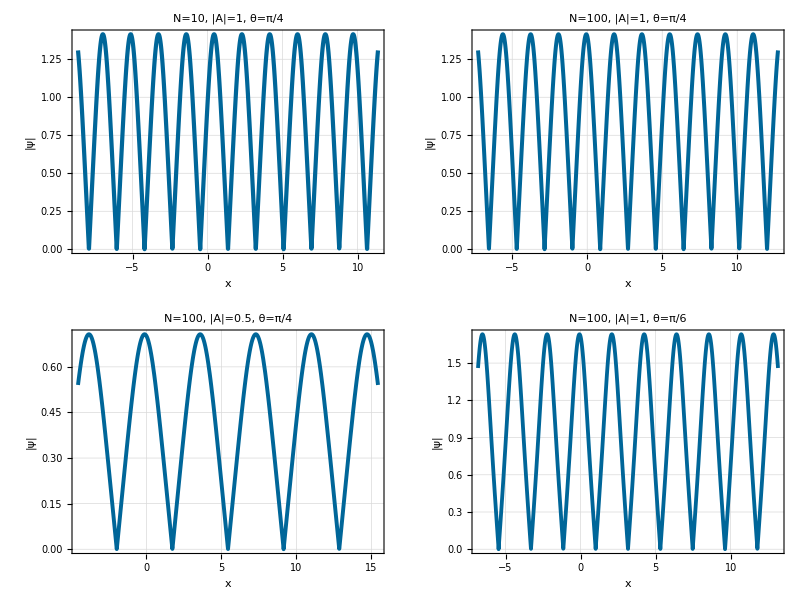

```mathematica
(*1. Define the Modulus of the Asymptotic Solution*)(*parameters:x (space),nSol (N),magA (|A|),theta (Arg(A))*)PsiAsympMod[x_,nSol_,magA_,theta_]:=Module[{prefactor,k,m,Kval,shift,u,sdVal},(*Calculate Pre-factor Magnitude: |-2i Re(A)Im(A)/|A|| -> |A|*|Sin(2 theta)|*)prefactor=magA*Abs[Sin[2*theta]];
(*Setup Elliptic Parameters*)(*Theorem uses k=cos(theta).Mathematica uses m=k^2*)k=Cos[theta];
m=k^2;
(*Complete Elliptic Integral K(m)*)Kval=EllipticK[m];
(*Calculate Argument u for JacobiSD*)(*u=-2|A|x+(2 K(cos(theta))/pi)*ln(N)*)shift=(2*Kval/Pi)*Log[nSol];
u=-2*magA*x+shift;
(*Calculate Jacobi SD function*)sdVal=JacobiSD[u,m];
(*Return Modulus*)prefactor*Abs[sdVal]];

(*2. Define Test Cases*)
(*Format:{N, |A|,theta,Label}*)
cases={{10,1.0,Pi/4,"N=10, |A|=1, θ=π/4"},{100,1.0,Pi/4,"N=100, |A|=1, θ=π/4"},{100,0.5,Pi/4,"N=100, |A|=0.5, θ=π/4"},{100,1.0,Pi/6,"N=100, |A|=1, θ=π/6"}};

(*Helper to center the plot window on the wave packet*)
GetCenter[nSol_,magA_,theta_]:=Module[{m,Kval,shift},m=Cos[theta]^2;
Kval=EllipticK[m];
shift=(2*Kval/Pi)*Log[nSol];
shift/(2*magA)];

(*3. Generate Plots*)
plots=Table[With[{n=case[[1]],a=case[[2]],th=case[[3]],lbl=case[[4]]},Module[{centerX},centerX=GetCenter[n,a,th];
Plot[PsiAsympMod[x,n,a,th],{x,centerX-10,centerX+10},(*Window+/-10 around center*)PlotRange->All,Frame->True,FrameLabel->{"x","|ψ|"},PlotLabel->Style[lbl,12,FontFamily->"Arial"],PlotStyle->{Thickness[0.006],RGBColor[0,0.4,0.6]},GridLines->Automatic,ImageSize->300]]],{case,cases}];

(*4. Display*)
Grid[Partition[plots,2],Spacings->{2,2}]
```

```mathematica
(*1. Define the Modulus Function*)PsiAsympMod[x_,nSol_,magA_,theta_]:=Module[{prefactor,k,m,Kval,shift,u,sdVal},prefactor=magA*Abs[Sin[2*theta]];
k=Cos[theta];
m=k^2;
Kval=EllipticK[m];
shift=(2*Kval/Pi)*Log[nSol];
u=-2*magA*x+shift;
sdVal=JacobiSD[u,m];
prefactor*Abs[sdVal]];

(*2. Define Cases*)
cases={{100,1.0,Pi/4,"N=100, |A|=1, θ=π/4","N100_A1_ThPi4"},{1000,1.0,Pi/4,"N=1000, |A|=1, θ=π/4","N1000_A1_ThPi4"},{1000,0.5,Pi/4,"N=1000, |A|=0.5, θ=π/4","N1000_A05_ThPi4"},{1000,1.0,Pi/6,"N=1000, |A|=1, θ=π/6","N1000_A1_ThPi6"}};

(*Helper to center the plot*)
GetCenter[nSol_,magA_,theta_]:=Module[{m,Kval,shift},m=Cos[theta]^2;
Kval=EllipticK[m];
shift=(2*Kval/Pi)*Log[nSol];
shift/(2*magA)];

(*3. Generate and Save Loop*)
(*Set the directory where you want to save.By default,this saves to your Notebook's current directory.*)
SetDirectory[NotebookDirectory[]];

Do[With[{n=case[[1]],a=case[[2]],th=case[[3]],title=case[[4]],fname=case[[5]]},Module[{centerX,plt},centerX=GetCenter[n,a,th];
plt=Plot[PsiAsympMod[x,n,a,th],{x,centerX-10,centerX+10},(*Styling for Publication*)PlotRange->All,Frame->True,FrameLabel->{Style["x",FontSize->16,FontSlant->Italic],Style["|ψ|",FontSize->16,FontSlant->Italic]},(*If you prefer NO title inside the plot for the paper,comment out PlotLabel*)PlotLabel->Style[title,14,FontFamily->"Times"],(*Professional Line Style*)PlotStyle->{AbsoluteThickness[2],RGBColor[0,0.2,0.5]},(*Dark blue is print-safe*)(*Ticks and Grid*)FrameTicksStyle->Directive[FontSize->12,FontFamily->"Times"],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],(*Aspect Ratio and Size*)ImageSize->400,(*Good width for single column figures*)BaseStyle->{FontFamily->"Times",FontSize->14}];
(*Export as PDF (Vector-Best for LaTeX)*)Export["Plot_"<>fname<>".pdf",plt];
(*Optional:Export as High-Res PNG if needed for slides*)(*Export["Plot_"<>fname<>".png",plt,ImageResolution->600];*)Print["Saved: Plot_"<>fname<>".pdf"];]],{case,cases}];
```

Saved: Plot_N100_A1_ThPi4.pdf

Saved: Plot_N1000_A1_ThPi4.pdf

Saved: Plot_N1000_A05_ThPi4.pdf

Saved: Plot_N1000_A1_ThPi6.pdf